## Constructing the Matrix Corresponding to the Derivative Operator, on the Full Basis and Sparse Basis 2D Inhomogenous Boundary Conditions

### Standard Definitions

```mathematica
ϕ[x_]:=If[Abs[x]>1,0,1-Abs[x]]
ϕ[l_,i_]:=If[l==-1,1,If[l==0,#,ϕ[2^l(#-2^-l(2i-1))]]]&
ϕ[lx_,ly_,i_,j_]:=ϕ[lx,i][#1]ϕ[ly,j][#2]&
ψ[lx_,ly_,i_,j_]:=ϕ[2^lx(#1-2^-lx i)]ϕ[2^ly(#2-2^-ly j)]&
ceil[x_,l_]:=If[x≥1,2^(l-1),1+Floor[2^(l-1)x]]
switch[x_]:=If[x≥1,x,1]
dϕ[x_]:=If[Abs[x]>1,0,
			If[x==1 ,-1/2,
			If[x==-1,1/2,
			If[x==0,0,
			If[x>0,-1,1]]]]](* Don't think I need this*)
```

### Test Functions, if you like

```mathematica
test2D[x_,y_]:=Cos[Pi x]^2Cos[Pi y]^2
test2D2[x_,y_]:=Sin[x+y]
dytest2D[x_,y_]:=2Pi Sin[Pi x]^2 Sin[Pi y] Cos[Pi y]
```

### Standard Basis

```mathematica
standardCoefficients2D[f_,lx_,ly_]:=Table[f[2^-lx i,2^-ly j],{i,0,2^lx},{j,0,2^ly}]
standardReconstruct2D[coefficients_,lx_,ly_]:=Sum[coefficients[[i+1,j+1]] ψ[lx,ly,i,j][#1,#2],{i,0,2^lx},{j,0,2^ly}]&

standardProject2D[f_,lx_,ly_]:=standardReconstruct2D[standardCoefficients2D[f,lx,ly],lx,ly]
```

### Full Basis

```mathematica
getCoefficient[f_,x_,l_]:=If[l==-1,f[0],If[l==0,f[1]-f[0],f[x]-1/2 f[x+2^-l]-1/2 f[x-2^-l]]]

getCoefficient2D[f_,x_,y_,lx_,ly_]:=getCoefficient[Function[y1,getCoefficient[Function[x1,f[x1,y1]],x,lx]],y,ly]
(* Tensor product construction
*)

fullCoefficients2D[f_,lx_,ly_]:=Table[Table[getCoefficient2D[f,2^-kx i,2^-ky j,kx,ky],{i,1,2^switch[kx]-1,2},{j,1,2^switch[ky]-1,2}],{kx,-1,lx},{ky,-1,ly}]


Reconstruct2D[coefficients_]:= Sum[coefficients[[kx+2,ky+2,ceil[#1,switch[kx]],ceil[#2,switch[ky]]]] 
ϕ[kx,ky,ceil[#1,switch[kx]],ceil[#2,switch[ky]]][#1,#2]
,{kx,-1,Length[coefficients]-2},{ky,-1,Length[coefficients]-2}]&
(*
Sum[coefficients[[lx+2,ly+2,ceil[#1,switch[lx]],ceil[#2,switch[ly]]]] ϕ[lx,ly,ceil[#1,switch[lx]],ceil[#2,switch[ly]]][#1,#2],{lx,-1,Length[coefficients]-2},{ly,-1,Length[coefficients[[lx]]]-2}]&
*)

reverseFlatten[coefficients_,kx_,ky_]:=Module[{k},k=0;Return[Table[Table[coefficients[[++k]] ,{i,1,2^(switch[lx]-1)},{j,1,2^(switch[ly]-1)}],{lx,-1,kx},{ly,-1,ky}]];]
(*Need to make this one work*)

project2D[f_,lx_,ly_]:=Reconstruct2D[fullCoefficients2D[f,lx,ly]]
```

```mathematica
Plot3D[test2D2[x,y]-#[x,y],{x,0,1},{y,0,1}]&@project2D[test2D2,3,3]
```

-Graphics3D-

### Sparse Basis

```mathematica
sparseCoefficients2D[f_,n_]:=Table[Table[Table[getCoefficient2D[f,2^-row i,2^(-(diag-row-1)) j,row,(diag-row-1)],{i,1,2^switch[row]-1,2},{j,1,2^switch[diag-row-1]-1,2}],{row,-1,diag}],{diag,-1,n}]

sparseReconstruct[coefficients_]:=Sum[Sum[coefficients[[diag+2,row+2,ceil[#1,switch[row]],ceil[#2,switch[diag-row-1]]]] 
ϕ[row,diag-row-1,ceil[#1,switch[row]],ceil[#2,switch[diag-row-1]]][#1,#2]
,{row,-1,diag}],{diag,-1,Length[coefficients]-2}]&

sparseProject[f_,n_]:=sparseReconstruct[sparseCoefficients2D[f,n]]
```

```mathematica
Plot3D[#[x,y],{x,0,1},{y,0,1}]&@sparseReconstruct[sparseCoefficients2D[test2D,8]//N]
```

-Graphics3D-

### Differentiation

```mathematica
diffx[f_,l_]:=
If[#1< 2^-l,(f[#1+2^(-l-1),#2]-f[#1,#2])/2^-l,If[#1> 1-2^-l,(f[#1,#2]-f[#1-2^(-l-1),#2])/2^-l,(f[#1+2^-l,#2]-f[#1-2^-l,#2])/(2 2^-l) ]]&(*If[#1< 2^-l, diffx[diffx[f,l+1],l+1][2^-l,#2]#1,If[#1> 1-2^-l, diffx[diffx[f,l+1],l+1][1-2^-l,#2](#1-1),(f[#1+2^-l,#2]-f[#1-2^-l,#2])/(2 2^-l) ]]&*)

diffy[f_,l_]:=
If[#1< 2^-l,(f[#1+2^(-l-1),#2]-f[#1,#2])/2^-l,If[#1> 1-2^-l,(f[#1,#2]-f[#1-2^(-l-1),#2])/2^-l,(f[#1+2^-l,#2]-f[#1-2^-l,#2])/(2 2^-l) ]]&(*If[#2< 2^-l, diffy[diffy[f,l+1],l+1][#1,2^-l]#2,If[#2> 1-2^-l, diffy[diffy[f,l+1],l+1][#1,1-2^-l](#2-1),(f[#1,#2+2^-l]-f[#1,#2-2^-l])/(2 2^-l)]]&*)
```

### Algorithms to form the Matrices

```mathematica
dxMatrix[lx_,ly_]:=Table[Table[fullCoefficients2D[diffx[ϕ[kx,ky,i,j],lx],lx,ly]//Flatten,{i,1,2^(switch[kx]-1)},{j,1,2^(switch[ky]-1)}],{kx,-1,lx},{ky,-1,ly}]
dyMatrix[lx_,ly_]:=Table[Table[fullCoefficients2D[diffy[ϕ[kx,ky,i,j],lx],lx,ly]//Flatten,{i,1,2^(switch[kx]-1)},{j,1,2^(switch[ky]-1)}],{kx,-1,lx},{ky,-1,ly}]


dxMatrixStandard[lx_,ly_]:=Table[standardCoefficients2D[diffx[ψ[lx,ly,i,j],lx],lx,ly]//Flatten,{i,0,2^lx},{j,0,2^ly}]
dyMatrixStandard[lx_,ly_]:=Table[standardCoefficients2D[diffy[ψ[lx,ly,i,j],lx],lx,ly]//Flatten,{i,0,2^lx},{j,0,2^ly}]


dxMatrixSparse[n_]:=Table[Table[Table[sparseCoefficients2D[diffx[ϕ[row,diag-row-1,i,j],n],n]//Flatten,{i,1,2^(switch[row]-1)},{j,1,2^(switch[diag-row-1]-1)}],{row,-1,diag}],{diag,-1,n}]

dyMatrixSparse[n_]:=Table[Table[Table[sparseCoefficients2D[diffy[ϕ[row,diag-row-1,i,j],n],n]//Flatten,{i,1,2^(switch[row]-1)},{j,1,2^(switch[diag-row-1]-1)}],{row,-1,diag}],{diag,-1,n}]
```

-Graphics-

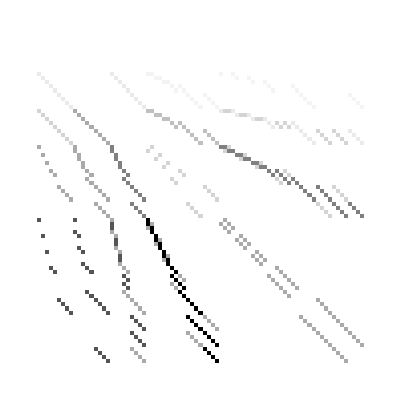

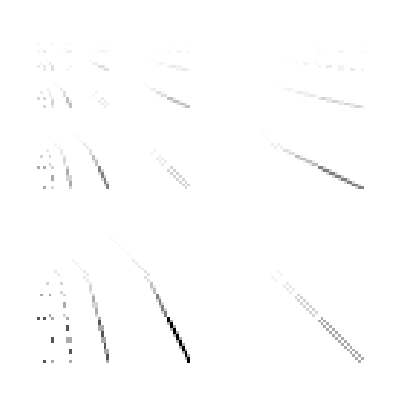

```mathematica
Flatten[dxMatrixStandard[3,3],1]//ArrayPlot
Flatten[dxMatrix[3,3],3]//ArrayPlot
Flatten[dxMatrixSparse[5],3]//ArrayPlot
```

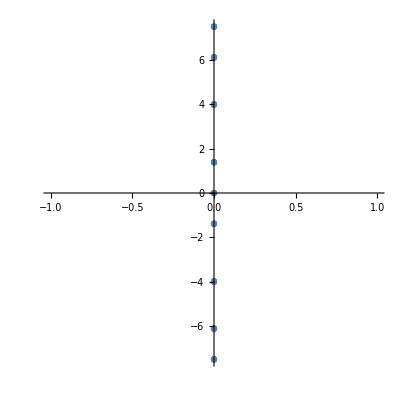

-Graphics-

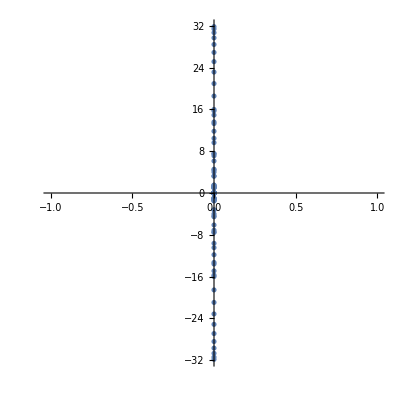

```mathematica
ListPlot[(Tooltip[{Re[#1],Im[#1]}]&)/@SetAccuracy[Flatten[dxMatrixStandard[3,3],1]//N//Eigenvalues,3],AspectRatio->1]
ListPlot[(Tooltip[{Re[#1],Im[#1]}]&)/@SetAccuracy[Flatten[dxMatrix[3,3],3]//N//Eigenvalues,3],AspectRatio->1]
ListPlot[(Tooltip[{Re[#1],Im[#1]}]&)/@SetAccuracy[Flatten[dxMatrixSparse[5],3]//N//Eigenvalues,3],AspectRatio->1]
```